```mathematica
ClearAll[f]
```

```mathematica
f[s_]:= (G ((1+δ)^s+1))/((1-δ)^s+1)
```

```mathematica
Expand[f[3]]
```

(2 G)/(1+(1-δ)^3)+(3 G δ)/(1+(1-δ)^3)+(3 G δ^2)/(1+(1-δ)^3)+(G δ^3)/(1+(1-δ)^3)

```mathematica
Series[(G ((1+δ)^s+1))/((1-δ)^s+1),{δ,0,2}]
```

G+G s δ+1/2 G s^2 δ^2+O[δ]^3

```mathematica
Solve[1/2 n x^2+n x-1==0, x]
```

{{x→(-n-√n √(2+n))/n},{x→(-n+√n √(2+n))/n}}

```mathematica
ω13 = 8000.;
ω0 = 12566.;
δ = ω0/ω13;
kBT = 0.695 6000;
```

```mathematica
Exp[ω13/kBT]
```

6.8105

```mathematica
Occ[ω_]:= (Exp[ω/(0.695 6000.)]-1)^-1
```

```mathematica
Occ[ω_]:= (Exp[ω/kBT]-1)^-1
```

```mathematica
n =Occ[ω13];
```

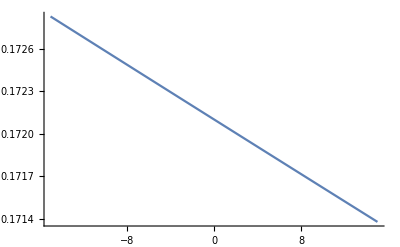

```mathematica
ListLinePlot[Table[{x,Occ[8000+x]},{x,-15,15}]]
```

```mathematica
s =(-n-√n √(2+n))/(δ n)
(s =-n+√n √(2+n))/(δ n)
```

-2.89836

1.62509

```mathematica
Clear[ω13, kBT]
```

```mathematica
Γ0[δω_]:= Occ[ω13+ δω]/(1+Occ[ω13 -δω]);
```

```mathematica
FullSimplify[D[Series[Γ0[δω], {δω, 0, 1}], δω]]
```

(1+ⅇ^(-ω13/kBT))/(kBT-ⅇ^(ω13/kBT) kBT)+O[δω]^1

```mathematica
ClearAll[f, ω13, δω]
```

```mathematica
P[s_, ω13_, δω_]:= (Occ[ω13+ δω]((ω13+δω)/ω13)^s+Occ[ω13])/((1+Occ[ω13 -δω])((ω13-δω)/ω13)^s+(Occ[ω13]+1));
```

```mathematica
Pa[s_, ω13_, δω_]:= (Occ[ω13]((ω13+δω)/ω13)^s+Occ[ω13])/((1+Occ[ω13])((ω13-δω)/ω13)^s+(Occ[ω13]+1));
```

(1/(-1+ⅇ^(ω13/kBT))+((δω+ω13)/ω13)^s/(-1+ⅇ^(ω13/kBT)))/(1+1/(-1+ⅇ^(ω13/kBT))+(1+1/(-1+ⅇ^(ω13/kBT))) ((-δω+ω13)/ω13)^s)

```mathematica
ClearAll[s, f, ω13, δω, kBT]
```

```mathematica
(1-e^-x)/e^-x
```

e^x (1-e^-x)

```mathematica
FullSimplify[Series[P[s, ω13, δω], {δω, 0,1}]]
```

ⅇ^(-ω13/kBT)+(ⅇ^(-ω13/kBT) (2 kBT s-ω13 Coth[ω13/(2 kBT)]) δω)/(2 kBT ω13)+O[δω]^2

```mathematica
ⅇ^(-ω13/kBT)+(ⅇ^(-ω13/kBT) (2 kBT s-ω13 Coth[ω13/(2 kBT)]) δω)/(2 kBT ω13)+((ⅇ^(-ω13/kBT) kBT s (2 kBT s+ω13)+(ω13 (4 kBT s+ω13+ⅇ^(ω13/kBT) (-4 kBT s+ω13)))/((-1+ⅇ^(ω13/kBT))^2)) δω^2)/(4 kBT^2 ω13^2)+O[δω]^3
```

```mathematica
FullSimplify[Solve[D[Series[P[s, ω13, δω], {δω, 0, 1}],δω]==0, s]]
```

{{s→(ω13 Coth[ω13/(2 kBT)])/(2 kBT)}}

```mathematica
Series[Pa[s, ω13, δω], {δω, 0, 1}]
```

ⅇ^(-ω13/kBT)+(ⅇ^(-ω13/kBT) s δω)/ω13+O[δω]^2

```mathematica
sMin[ω13_, kBT_]:=((1+ⅇ^(ω13/kBT)) ω13)/(2 (-1+ⅇ^(ω13/kBT)) kBT)
```

```mathematica
FullSimplify[sMin[ω13, kBT]]
```

(ω13 Coth[ω13/(2 kBT)])/(2 kBT)

```mathematica
Limit[sMin[ω13, kBT],
```

```mathematica
kBT=0.695 6000.;
ω13 = 8000.;
```

```mathematica
s=((1+ⅇ^(ω13/kBT)) ω13)/(2 (-1+ⅇ^(ω13/kBT)) kBT)
```

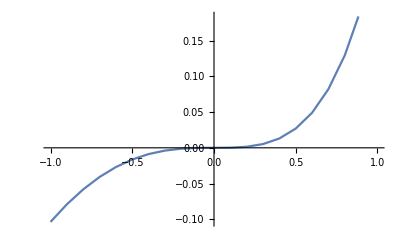

```mathematica
f[x_]:=x+(x-2)Exp[x]+2
ListLinePlot[Table[{n, f[n]},{n,-1,1, 0.1}]]
```

```mathematica
Solve[D[P[s,8000., x], x]==0., s]
```

$Aborted

```mathematica
P[3, 6000, 5]
```

0.237563

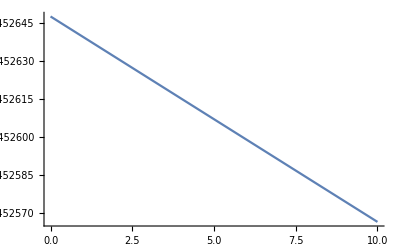

```mathematica
ListLinePlot[Table[{n,P[s,8066,n]},{n,0,10}]]
```

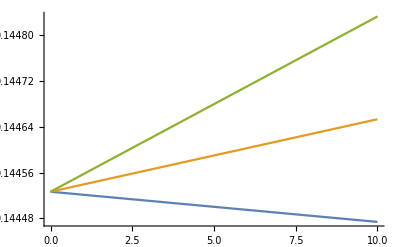

```mathematica
ListLinePlot[Table[{n,P[s,8066,n]},{s,3},{n,0,10}]]
```

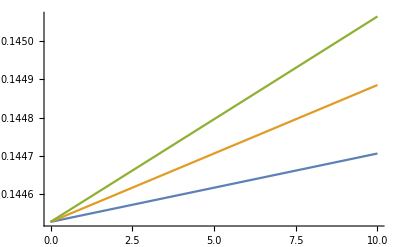

```mathematica
ListLinePlot[Table[{n,Pa[s,8066,n]},{s,3},{n,0,10}]]
```

```mathematica
Solve[P[s, ω13, δω]==0, s]
```

Solve[(1/(-1+ⅇ^(0.000239808 ω13))+((δω+ω13)/ω13)^0.439309/(-1+ⅇ^(0.000239808 (δω+ω13))))/(1+1/(-1+ⅇ^(0.000239808 ω13))+(1+1/(-1+ⅇ^(0.000239808 (-δω+ω13)))) ((-δω+ω13)/ω13)^0.439309)==0,0.439309]